```mathematica
(*Transcription and Translation*)
```

```mathematica
ao=59.5122;at=1;

(*Binding/Unbinding*)
kcf=4.76011;kpf=4.28606;kppf=7.31679;
Kcbo=0.0000392194;Kcbt=0.000114715176224;Kcbh=1.3118850080599999*^-8;
Kpb=2.01252;Kppb=0.0694476;
Kd=0.0000155496;

(*Phosphorylation Rate*)
kpo=9.112619522;kp=0.694004;kr=6.03311;

(*Dephosphorylation Rate*)
kppo=28.165567051799997;kpp=9.60846;

(*Degradation/Ubiquitination*)
do=0.242241;
bo=0.000676569;bt=73.1566;bh=0.339140359785;
ub=655.913;

(*Abuandance*)
CKt=146.245;PRt=16.5311; PPt=11.5037;ACt=1.36596;
(*CHX*)
tld=4.81992;
endt=300;
```

```mathematica
endt=300;

(*Simulation of circadina rhythms*)
aone=
{
m'[t] == ao*(1 - ( c4[t] + 
            c4PP[t]+c4CK[t])/AC[t] - Kd/AC[t] + 
      Sqrt[(1 - ( c4[t] + 
            c4PP[t]+c4CK[t])/AC[t] - Kd/AC[t])^2 + 4*Kd/AC[t]])/2 - 
  do*m[t],

c0'[t]==at*m[t]-kcf*c0[t]*CK[t]+Kcbo*c0CK[t]-kpf*c0[t]*PR[t]+Kpb*c0PR[t]+kpp*c1PP[t]+kppo*ct1PP[t]-bo*c0[t],
c0CK'[t]==kcf*c0[t]*CK[t]-(Kcbo+kpo+bo)*c0CK[t],
c0PR'[t]==kpf*c0[t]*PR[t]-(Kpb+kr+bo)*c0PR[t],


ct1'[t]==kpo*c0CK[t]-kppf*ct1[t]*PP[t]+Kppb*ct1PP[t]-(ub+bo)*ct1[t],
ct1PP'[t]==kppf*ct1[t]*PP[t]-(Kppb+ub+bo+kppo)*ct1PP[t],

c1'[t]==kr*(c0PR[t])-kppf*c1[t]*PP[t]+Kppb*c1PP[t]-kcf*c1[t]*CK[t]+Kcbt*c1CK[t]-bo*c1[t]+kpp*c2PP[t],
c1PP'[t]==kppf*c1[t]*PP[t]-(Kppb+bo+kpp)*c1PP[t],
c1CK'[t]==kcf*c1[t]*CK[t]-(Kcbt+kp+bo)*c1CK[t],

c2'[t]==kp*c1CK[t]-kppf*c2[t]*PP[t]+Kppb*c2PP[t]-kcf*c2[t]*CK[t]+Kcbt*c2CK[t]-bo*c2[t]+kpp*c3PP[t],
c2PP'[t]==kppf*c2[t]*PP[t]-(Kppb+bo+kpp)*c2PP[t],
c2CK'[t]==kcf*c2[t]*CK[t]-(Kcbt+kp+bo)*c2CK[t],

c3'[t]==kp*c2CK[t]-kppf*c3[t]*PP[t]+Kppb*c3PP[t]-kcf*c3[t]*CK[t]+Kcbh*c3CK[t]-bo*c3[t]+kpp*c4PP[t],
c3PP'[t]==kppf*c3[t]*PP[t]-(Kppb+bo+kpp)*c3PP[t],
c3CK'[t]==kcf*c3[t]*CK[t]-(Kcbh+kp+bo)*c3CK[t],

c4'[t]==kp*c3CK[t]-kppf*c4[t]*PP[t]+Kppb*c4PP[t]-kcf*c4[t]*CK[t]+Kcbh*c4CK[t]-bh*c4[t],
c4PP'[t]==kppf*c4[t]*PP[t]-(Kppb+bh+kpp)*c4PP[t],
c4CK'[t]==kcf*c4[t]*CK[t]-(Kcbh+bh)*c4CK[t],

cub'[t]==ub*(ct1[t]+ct1PP[t])-bt*cub[t],

CK'[t]==-kcf*CK[t]*(c0[t]+c1[t]+c2[t]+c3[t]+c4[t])+(kpo+bo)*(c0CK[t])+(kp+bo)*(c1CK[t]+c2CK[t]+c3CK[t])+
bh*c4CK[t]+Kcbo*c0CK[t]+Kcbt*(c1CK[t]+c2CK[t])+Kcbh*(+c3CK[t]+c4CK[t]),
PR'[t]==-kpf*(c0[t])*PR[t]+(Kpb+kr+bo)*c0PR[t],
PP'[t]==-kppf*PP[t]*(ct1[t]+c1[t]+c2[t]+c3[t]+c4[t])+(Kppb+kpp+bo)*(c1PP[t]+c2PP[t]+c3PP[t])+(Kppb+kppo+bo)*ct1PP[t]+(Kppb+kpp+bh)*c4PP[t]+ub*ct1PP[t],


AC'[t]==0};


atwo={m[0]==0,c0[0]==0,c0CK[0]==0,c0PR[0]==0,ct1[0]==0,ct1PP[0]==0,c1[0]==0,c1PP[0]==0,c1CK[0]==0,c2[0]==0,c2PP[0]==0,c2CK[0]==0,c3[0]==0,c3PP[0]==0,c3CK[0]==0,c4[0]==0,c4PP[0]==0,c4CK[0]==0,cub[0]==0,CK[0]==CKt,PR[0]==PRt,PP[0]==PPt,AC[0]==ACt};
afive={m,c0,c0CK,c0PR,ct1,ct1PP,c1,c1PP,c1CK,c2,c2PP,c2CK,c3,c3PP,c3CK,c4,c4PP,c4CK,cub,CK,PR,PP,AC};

qtm=NDSolve[Join[aone,atwo],afive,{t,0,endt},MaxSteps->10000000,MaxStepSize->0.01];
```

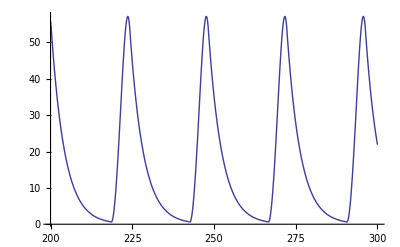

```mathematica
Plot[{m[t]/.qtm},{t,200,300},PlotRange->All]
```

```mathematica
(*CHX simulation*)
```

```mathematica
(*Period menasurment*)
omax=t/.Last[FindMaximum[m[t]/.qtm,{t,endt-30,endt}]];
tmax=t/.Last[FindMaximum[m[t]/.qtm,{t,omax-25,omax-5}]];
pper=omax-tmax
```

24.0171

```mathematica
(*PER2 peak and bottom time*)
```

```mathematica
k[t_]:=c0[t]+c0CK[t]+c0PR[t]+ct1[t]+ct1PP[t]+c1[t]+c1PP[t]+c1CK[t]+c2[t]+c2PP[t]+c2CK[t]+c3[t]+c3PP[t]+c3CK[t]+c4[t]+c4PP[t]+c4CK[t]+cub[t] (*Total protein function)
```

```mathematica
endtt=pper*2;
XY=Table[k[t]/.qtm[[1]],{t,endt-pper*2,endt-pper,0.1}];
hmax=endt-pper*2+Position[XY,Max[XY]][[1]][[1]]*0.1;
XY=Table[k[t]/.qtm[[1]],{t,hmax-pper,hmax,0.1}];
hmin=hmax-pper+Position[XY,Min[XY]][[1]][[1]]*0.1;
```

```mathematica
(*Note that tl[t] represents the exponential decrease of translation rate by CHX*)
aonet=
{
m'[t] == ao*(1 - ( c4[t] + 
            c4PP[t]+c4CK[t])/AC[t] - Kd/AC[t] + 
      Sqrt[(1 - ( c4[t] + 
            c4PP[t]+c4CK[t])/AC[t] - Kd/AC[t])^2 + 4*Kd/AC[t]])/2 - 
  do*m[t],

c0'[t]==tl[t]*at*m[t]-kcf*c0[t]*CK[t]+Kcbo*c0CK[t]-kpf*c0[t]*PR[t]+Kpb*c0PR[t]+kpp*c1PP[t]+kppo*ct1PP[t]-bo*c0[t],
c0CK'[t]==kcf*c0[t]*CK[t]-(Kcbo+kpo+bo)*c0CK[t],
c0PR'[t]==kpf*c0[t]*PR[t]-(Kpb+kr+bo)*c0PR[t],


ct1'[t]==kpo*c0CK[t]-kppf*ct1[t]*PP[t]+Kppb*ct1PP[t]-(ub+bo)*ct1[t],
ct1PP'[t]==kppf*ct1[t]*PP[t]-(Kppb+ub+bo+kppo)*ct1PP[t],

c1'[t]==kr*(c0PR[t])-kppf*c1[t]*PP[t]+Kppb*c1PP[t]-kcf*c1[t]*CK[t]+Kcbt*c1CK[t]-bo*c1[t]+kpp*c2PP[t],
c1PP'[t]==kppf*c1[t]*PP[t]-(Kppb+bo+kpp)*c1PP[t],
c1CK'[t]==kcf*c1[t]*CK[t]-(Kcbt+kp+bo)*c1CK[t],

c2'[t]==kp*c1CK[t]-kppf*c2[t]*PP[t]+Kppb*c2PP[t]-kcf*c2[t]*CK[t]+Kcbt*c2CK[t]-bo*c2[t]+kpp*c3PP[t],
c2PP'[t]==kppf*c2[t]*PP[t]-(Kppb+bo+kpp)*c2PP[t],
c2CK'[t]==kcf*c2[t]*CK[t]-(Kcbt+kp+bo)*c2CK[t],

c3'[t]==kp*c2CK[t]-kppf*c3[t]*PP[t]+Kppb*c3PP[t]-kcf*c3[t]*CK[t]+Kcbh*c3CK[t]-bo*c3[t]+kpp*c4PP[t],
c3PP'[t]==kppf*c3[t]*PP[t]-(Kppb+bo+kpp)*c3PP[t],
c3CK'[t]==kcf*c3[t]*CK[t]-(Kcbh+kp+bo)*c3CK[t],

c4'[t]==kp*c3CK[t]-kppf*c4[t]*PP[t]+Kppb*c4PP[t]-kcf*c4[t]*CK[t]+Kcbh*c4CK[t]-bh*c4[t],
c4PP'[t]==kppf*c4[t]*PP[t]-(Kppb+bh+kpp)*c4PP[t],
c4CK'[t]==kcf*c4[t]*CK[t]-(Kcbh+bh)*c4CK[t],

cub'[t]==ub*(ct1[t]+ct1PP[t])-bt*cub[t],

CK'[t]==-kcf*CK[t]*(c0[t]+c1[t]+c2[t]+c3[t]+c4[t])+(kpo+bo)*(c0CK[t])+(kp+bo)*(c1CK[t]+c2CK[t]+c3CK[t])+
bh*c4CK[t]+Kcbo*c0CK[t]+Kcbt*(c1CK[t]+c2CK[t])+Kcbh*(+c3CK[t]+c4CK[t]),
PR'[t]==-kpf*(c0[t])*PR[t]+(Kpb+kr+bo)*c0PR[t],
PP'[t]==-kppf*PP[t]*(ct1[t]+c1[t]+c2[t]+c3[t]+c4[t])+(Kppb+kpp+bo)*(c1PP[t]+c2PP[t]+c3PP[t])+(Kppb+kppo+bo)*ct1PP[t]+(Kppb+kpp+bh)*c4PP[t]+ub*ct1PP[t],


AC'[t]==0,
tl'[t]==-tld*tl[t]};
```

```mathematica
(*CHX treatment at different circadain phases*)
chxt=hmin+(hmax-hmin)/4;
Inito={m[0],c0[0],c0CK[0],c0PR[0],ct1[0],ct1PP[0],c1[0],c1PP[0],c1CK[0],c2[0],c2PP[0],c2CK[0],c3[0],c3PP[0],c3CK[0],c4[0],c4PP[0],c4CK[0],cub[0],CK[0],PR[0],PP[0],AC[0],tl[0]};
Initt=Join[{m[chxt],c0[chxt],c0CK[chxt],c0PR[chxt],ct1[chxt],ct1PP[chxt],c1[chxt],c1PP[chxt],c1CK[chxt],c2[chxt],c2PP[chxt],c2CK[chxt],c3[chxt],c3PP[chxt],c3CK[chxt],c4[chxt],c4PP[chxt],c4CK[chxt],cub[chxt],CK[chxt],PR[chxt],PP[chxt],AC[chxt]}/.qtm[[1]],{1}];
atwot=Table[Inito[[jj]]==Initt[[jj]],{jj,1,Length[Inito]}];
afive={m,c0,c0CK,c0PR,ct1,ct1PP,c1,c1PP,c1CK,c2,c2PP,c2CK,c3,c3PP,c3CK,c4,c4PP,c4CK,cub,CK,PR,PP,AC,tl};
qtt=NDSolve[Join[aonet,atwot],afive,{t,0,15},MaxSteps->10000000,MaxStepSize->0.01];


chxt=hmin+(hmax-hmin)/2;
Inito={m[0],c0[0],c0CK[0],c0PR[0],ct1[0],ct1PP[0],c1[0],c1PP[0],c1CK[0],c2[0],c2PP[0],c2CK[0],c3[0],c3PP[0],c3CK[0],c4[0],c4PP[0],c4CK[0],cub[0],CK[0],PR[0],PP[0],AC[0],tl[0]};
Initt=Join[{m[chxt],c0[chxt],c0CK[chxt],c0PR[chxt],ct1[chxt],ct1PP[chxt],c1[chxt],c1PP[chxt],c1CK[chxt],c2[chxt],c2PP[chxt],c2CK[chxt],c3[chxt],c3PP[chxt],c3CK[chxt],c4[chxt],c4PP[chxt],c4CK[chxt],cub[chxt],CK[chxt],PR[chxt],PP[chxt],AC[chxt]}/.qtm[[1]],{1}];
atwot=Table[Inito[[jj]]==Initt[[jj]],{jj,1,Length[Inito]}];
afive={m,c0,c0CK,c0PR,ct1,ct1PP,c1,c1PP,c1CK,c2,c2PP,c2CK,c3,c3PP,c3CK,c4,c4PP,c4CK,cub,CK,PR,PP,AC,tl};
qttt=NDSolve[Join[aonet,atwot],afive,{t,0,15},MaxSteps->10000000,MaxStepSize->0.01];

chxt=hmin+(hmax-hmin)*3/4;
Inito={m[0],c0[0],c0CK[0],c0PR[0],ct1[0],ct1PP[0],c1[0],c1PP[0],c1CK[0],c2[0],c2PP[0],c2CK[0],c3[0],c3PP[0],c3CK[0],c4[0],c4PP[0],c4CK[0],cub[0],CK[0],PR[0],PP[0],AC[0],tl[0]};
Initt=Join[{m[chxt],c0[chxt],c0CK[chxt],c0PR[chxt],ct1[chxt],ct1PP[chxt],c1[chxt],c1PP[chxt],c1CK[chxt],c2[chxt],c2PP[chxt],c2CK[chxt],c3[chxt],c3PP[chxt],c3CK[chxt],c4[chxt],c4PP[chxt],c4CK[chxt],cub[chxt],CK[chxt],PR[chxt],PP[chxt],AC[chxt]}/.qtm[[1]],{1}];
atwot=Table[Inito[[jj]]==Initt[[jj]],{jj,1,Length[Inito]}];
afive={m,c0,c0CK,c0PR,ct1,ct1PP,c1,c1PP,c1CK,c2,c2PP,c2CK,c3,c3PP,c3CK,c4,c4PP,c4CK,cub,CK,PR,PP,AC,tl};
qtth=NDSolve[Join[aonet,atwot],afive,{t,0,15},MaxSteps->10000000,MaxStepSize->0.01];


chxt=hmax+(pper-(hmax-hmin))/4;
Inito={m[0],c0[0],c0CK[0],c0PR[0],ct1[0],ct1PP[0],c1[0],c1PP[0],c1CK[0],c2[0],c2PP[0],c2CK[0],c3[0],c3PP[0],c3CK[0],c4[0],c4PP[0],c4CK[0],cub[0],CK[0],PR[0],PP[0],AC[0],tl[0]};
Initt=Join[{m[chxt],c0[chxt],c0CK[chxt],c0PR[chxt],ct1[chxt],ct1PP[chxt],c1[chxt],c1PP[chxt],c1CK[chxt],c2[chxt],c2PP[chxt],c2CK[chxt],c3[chxt],c3PP[chxt],c3CK[chxt],c4[chxt],c4PP[chxt],c4CK[chxt],cub[chxt],CK[chxt],PR[chxt],PP[chxt],AC[chxt]}/.qtm[[1]],{1}];
atwot=Table[Inito[[jj]]==Initt[[jj]],{jj,1,Length[Inito]}];
afive={m,c0,c0CK,c0PR,ct1,ct1PP,c1,c1PP,c1CK,c2,c2PP,c2CK,c3,c3PP,c3CK,c4,c4PP,c4CK,cub,CK,PR,PP,AC,tl};
qth=NDSolve[Join[aonet,atwot],afive,{t,0,15},MaxSteps->10000000,MaxStepSize->0.01];

chxt=hmax+(pper-(hmax-hmin))/2;
Inito={m[0],c0[0],c0CK[0],c0PR[0],ct1[0],ct1PP[0],c1[0],c1PP[0],c1CK[0],c2[0],c2PP[0],c2CK[0],c3[0],c3PP[0],c3CK[0],c4[0],c4PP[0],c4CK[0],cub[0],CK[0],PR[0],PP[0],AC[0],tl[0]};
Initt=Join[{m[chxt],c0[chxt],c0CK[chxt],c0PR[chxt],ct1[chxt],ct1PP[chxt],c1[chxt],c1PP[chxt],c1CK[chxt],c2[chxt],c2PP[chxt],c2CK[chxt],c3[chxt],c3PP[chxt],c3CK[chxt],c4[chxt],c4PP[chxt],c4CK[chxt],cub[chxt],CK[chxt],PR[chxt],PP[chxt],AC[chxt]}/.qtm[[1]],{1}];
atwot=Table[Inito[[jj]]==Initt[[jj]],{jj,1,Length[Inito]}];
afive={m,c0,c0CK,c0PR,ct1,ct1PP,c1,c1PP,c1CK,c2,c2PP,c2CK,c3,c3PP,c3CK,c4,c4PP,c4CK,cub,CK,PR,PP,AC,tl};
qtht=NDSolve[Join[aonet,atwot],afive,{t,0,15},MaxSteps->10000000,MaxStepSize->0.01];
```

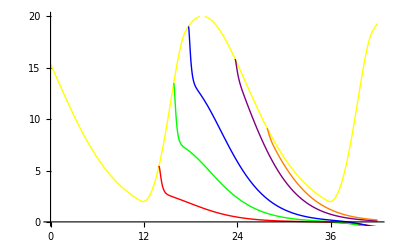

```mathematica
go[t_]:=k[t]/.qtm;
gt[t_]:=k[t]/.qtt;
gh[t_]:=k[t]/.qttt;
gf[t_]:=k[t]/.qtth;
gv[t_]:=k[t]/.qth;
gs[t_]:=k[t]/.qtht;

Show[Plot[go[t+hmin-12],{t,0,42},PlotStyle->{Thick,Yellow},AxesStyle->Directive[Thick,FontSize->20],
BaseStyle->{FontFamily->"Helvetica",FontSize->20},AxesOrigin->{0,0},Ticks->{{0,3,6,9,12,15,18,21,24}*2,{0,5,10,15,20}},PlotRange->{0,20}],
Plot[{gt[-(hmax-hmin)/4+t-12]},{t,(hmax-hmin)/4+12,42},PlotRange->All,PlotStyle->{Thick, Red}],
Plot[{gh[-(hmax-hmin)/2+t-12]},{t,(hmax-hmin)/2+12,42},PlotRange->All,PlotStyle->{Thick, Green}],Plot[{gf[-(hmax-hmin)*3/4+t-12]},{t,(hmax-hmin)*3/4+12,42},PlotRange->All,PlotStyle->{Thick,Blue}],Plot[{gv[-(hmax+(pper-(hmax-hmin))/4)+hmin+t-12]},{t,(hmax+(pper-(hmax-hmin))/4)-hmin+12,42},PlotRange->All,PlotStyle->{Thick, Purple}],Plot[{gs[-(hmax+(pper-(hmax-hmin))/2)+hmin+t-12]},{t,(hmax+(pper-(hmax-hmin))/2)-hmin+12,42},PlotRange->All,PlotStyle->{Thick, Orange}]]
```